# Light DM from Cosmic Rays

Following 1810.10543 Bringmann & Pospelov

Using parametrisation of local interstellar spectra (LIS) from 1704.06337 Boschini et al. Only use in rigidity range above 0.2 GV. 
Rigidity R units in GV
differential intensity proton flux in units of m^-2 s^-1 sr^-1 GV^-1

```mathematica
(*proton*)
dϕpLISdR[R_]:=Module[
{a0,a1,a2,a3,a4,a5,b,c,d1,d2,e1,e2,f1,f2,g,Fp1,Fp2},
{a0,a1,a2,a3,a4,a5}={94.1,-831,0,16700,-10200,0};
{b,c,d1,d2,e1,e2,f1,f2,g}={10800,8590,-4230000,3190,274000,17.4,-39400,0.464,0};
Fp1=a0+a1*R+a2*R^2+a3*R^3+a4*R^4+a5*R^5;
Fp2=b+c/R+d1/(d2+R)+e1/(e2+R)+f1/(f2+R)+g*R;
If[R≤ 1,Fp1/R^2.7,Fp2/R^2.7]
]
```

Check flux with Fig. 3 of  Boschini et al.

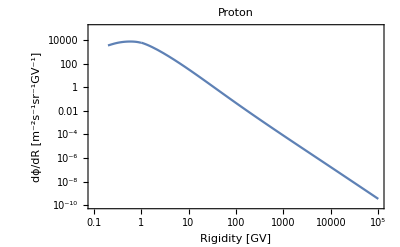

```mathematica
LogLogPlot[dϕpLISdR[R],{R,0.2,10^5},PlotRange->{{10^-1,10^5},{10^-10,10^5}},Frame->True,FrameLabel->{"Rigidity [GV]","dϕ/dR [m^-2s^-1sr^-1GV^-1]"},LabelStyle->FontSize->16,PlotLabel->"Proton"]
```

Parametrisation only works above this minimum rigidity value

```mathematica
minRprotonparam=0.2
```

0.2

Beware when using this parametrisation below R=0.2 GV (T=0.02 GeV)!

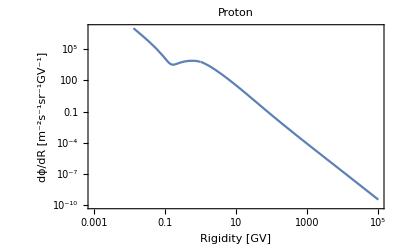

```mathematica
LogLogPlot[dϕpLISdR[R],{R,10^-4,10^5},PlotRange->{{10^-3,10^5},{10^-10,10^7}},Frame->True,FrameLabel->{"Rigidity [GV]","dϕ/dR [m^-2s^-1sr^-1GV^-1]"},LabelStyle->FontSize->16,PlotLabel->"Proton"]
```

Convert Rigidity to Kinetic Energy
A = atomic number
Z = charge
T = Kinetic energy per nucleon
T0 = rest energy

```mathematica
Rigidity[T_,T0_,A_,Z_]:=A/Z √(T^2+2*T*T0)
pMassGeV=0.938;
protonRigidity [T_]:=Rigidity[T,pMassGeV,1,1]

protondRdT[T_]:=(1.876+2 T)/(2 √(1.876 T+T^2))

protonTfromR[R_]:=Select[{0.002 (-469.-1. √(219961.+250000. R^2)),0.002 (-469.+√(219961.+250000. R^2))},Positive][[1]]

(*protondTdR[R_]:=(500. R)/(√(219961.+250000. R^2))*)
```

```mathematica
protonRigidity [T]
```

√(1.876 T+T^2)

```mathematica
D[protonRigidity [T],T]
```

(1.876+2 T)/(2 √(1.876 T+T^2))

```mathematica
Solve[protonRigidity[T]==R,T]
```

{{T→0.002 (-469.-1. √(219961.+250000. R^2))},{T→0.002 (-469.+√(219961.+250000. R^2))}}

Differential intensity proton flux for kinetic energy instead of rigidity in units of m^-2 s^-1 GeV^-1 (but not per unit angle)

```mathematica
dϕpLISdT[T_]:=4π*protondRdT[T]*dϕpLISdR[protonRigidity[T]]

minTprotonparam=protonTfromR[minRprotonparam]
```

0.021085

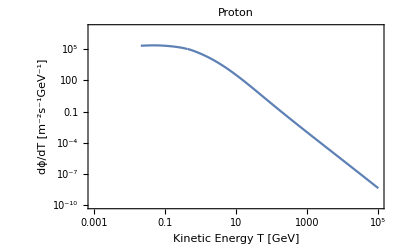

```mathematica
LogLogPlot[dϕpLISdT[T],{T,protonTfromR[0.2],10^5},PlotRange->{{10^-3,10^5},{10^-10,10^7}},Frame->True,FrameLabel->{"Kinetic Energy T [GeV]","dϕ/dT [m^-2s^-1GeV^-1]"},LabelStyle->FontSize->16,PlotLabel->"Proton"]
```

Dark matter flux in GeV^-1 cm^-2 s^-2

```mathematica
ρχlocalGeVinvcm3=0.3;
kpctocm=3.086*10^21;
m2tocm2=10^4;

dϕχdTproton[T_,σχcm2_,mχGeV_,Deffkpc_]:=σχcm2*ρχlocalGeVinvcm3/mχGeV*Deffkpc*kpctocm*dϕpLISdT[T]/m2tocm2
```

```mathematica
protonTχmax[T_,mχGeV_]:=(T^2+2*pMassGeV*T)/(T+(pMassGeV+mχGeV)^2/(2*mχGeV))

protonTmin[Tχ_,mχGeV_]:=If[Tχ>2*pMassGeV,(Tχ/2-pMassGeV)*(1+√(1+(2Tχ)/mχGeV*(pMassGeV+mχGeV)^2/(2*pMassGeV-Tχ)^2)),(Tχ/2-pMassGeV)*(1-√(1+(2Tχ)/mχGeV*(pMassGeV+mχGeV)^2/(2*pMassGeV-Tχ)^2))]

ΛprotonGeV=0.770;
protonGfactor[QGeV2_]:=1/((1+QGeV2/ΛprotonGeV^2)^2)

(*note we include a Theta function to avoid using proton kinetic energies below parametrisation validity*)
dϕχdTχ[Tχ_,σχcm2_,mχGeV_,Deffkpc_]:=protonGfactor[2*mχGeV*Tχ]^2*NIntegrate[dϕχdTproton[T,σχcm2,mχGeV,Deffkpc]*1/protonTχmax[T,mχGeV]*HeavisideTheta[protonTχmax[T,mχGeV]-Tχ]*HeavisideTheta[T-minTprotonparam],{T,protonTmin[Tχ,mχGeV],∞}]
```

```mathematica
10^-5*dϕχdTχ[10^-5,10^-30,1,8.02]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in T near {T} = {0.0211146}. NIntegrate obtained 4.85344×10^-7 and 3.47516×10^-11 for the integral and error estimates.

4.85279×10^-12

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in T near {T} = {0.0220199}. NIntegrate obtained 6.02719×10^-8 and 1.2812×10^-10 for the integral and error estimates.

LogLogPlot::exclul: {(1+3.37325 ⅇ^Tχ)-0,Im[-ⅇ^Tχ+(1.876 T+T^2)/(1.87792+T)]-0,(-ⅇ^Tχ+(1.876 T+T^2)/(1.87792+T))-0} must be a list of equalities or real-valued functions.

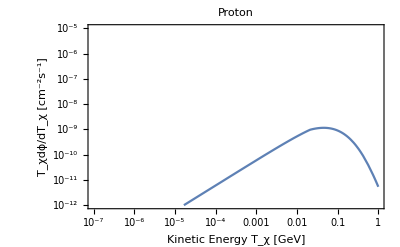

```mathematica
LogLogPlot[Tχ*dϕχdTχ[Tχ,10^-30,1.0,0.997],{Tχ,10^-6,1},PlotRange->{{10^-7,1},{10^-12,10^-5}},Frame->True,FrameLabel->{"Kinetic Energy T_χ [GeV]","T_χdϕ/dT_χ [cm^-2s^-1]"},LabelStyle->FontSize->16,PlotLabel->"Proton"]
```